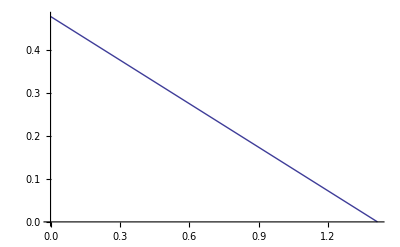

```mathematica
(* Gupta-Sproull *)
(* cone with linear decrease, radius √2; derive peak from the unit-integral property *)
(* cone volume = 1/3 π r^2 h *)
h = 3/π/2;
filtGS[x_] := If[x < √2, -(h/√2) x + h, 0]
Plot[filtGS[x], {x, 0, √2}]
```

0.675237

0.678171-0.103604 x-0.701975 x^2+0.306376 x^3

0.468971

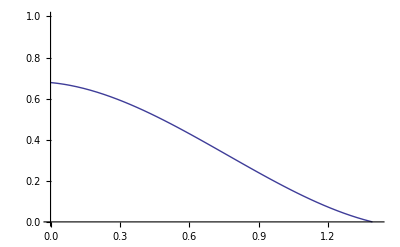

```mathematica
(* RLT - our derivation *)
transGS2[r_] := 2 NIntegrate[filtGS[Norm[{r,x}]], {x, 0, √2}]
transGS2[0]
steps = 100.0;
xAtStep[i_] := i √2 / steps
support = Table[0, {i,steps+1}, {j,2}];
For[i=0, i <= steps, i += 1, support[[i+1]] = {xAtStep[i], transGS2[xAtStep[i]]}]
interp = Fit[support, {1,x,x^2,x^3}, x]
Integrate[interp, {x, 0, 1}]
(* ListPlot[supportMN] *)
Plot[interp, {x, 0, √2}, PlotRange -> {0,1.0}]
```

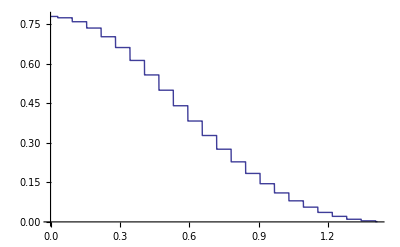

```mathematica
(* RLT - from [GS81]'s table *)
values = {0.780,0.775,0.760,0.736,0.703,0.662,0.613,0.558,0.500,0.441,0.383,0.328,0.276,0.228,0.184,0.145,0.110,0.080,0.056,0.036,0.021,0.010,0.004,0.001,0.000};
transGS[x_] := If[x ≤ √2, values[[Round[x*16]+1]],0]
Plot[transGS[x], {x, 0, √2}, PlotRange -> {0,1.0}]
```